## Create points

Uncomment the one you want to use. The results should be the same.

{0.,0.0010273,0.00410499,0.00922042,0.0163526,0.0254721,0.0365416,0.0495156,0.0643406,0.0809559,0.0992932,0.119277,0.140825,0.16385,0.188255,0.213942,0.240804,0.268731,0.297608,0.327317,0.357736,0.38874,0.4202,0.451988,0.483974,0.516026,0.548012,0.5798,0.61126,0.642264,0.672683,0.702392,0.731269,0.759196,0.786058,0.811745,0.83615,0.859175,0.880723,0.900707,0.919044,0.935659,0.950484,0.963458,0.974528,0.983647,0.99078,0.995895,0.998973,1.}

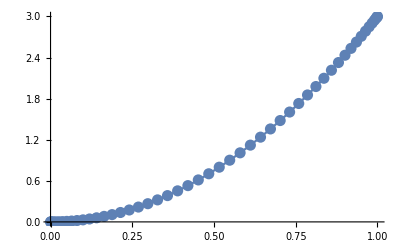

```mathematica
(*EvenlySpacedPointsFactory[points,0,1,50,z]*)
CollocationPointsFactory[points,0,1,50,z]
points[z]
points[diff][points[z]^3]//points[plot]
```

## Differentiate

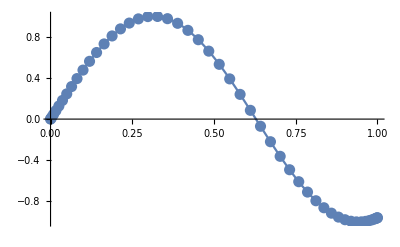

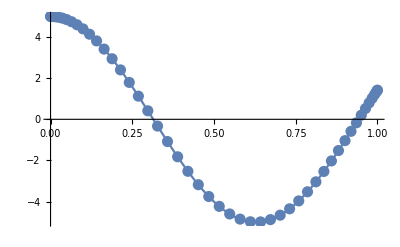

-Graphics-

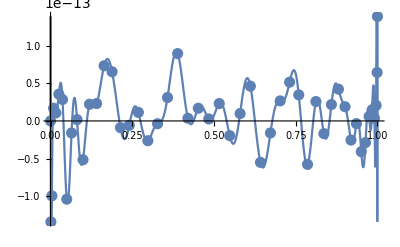

-Graphics-

```mathematica
points[plot][Sin[5points[z]],PlotRange->All]
points[plot][points[diff][Sin[5points[z]]]]
points[plot][points[diffMatrix][1].Sin[5points[z]]]
points[plot][points[diffMatrix][1].Sin[5points[z]]-5Cos[5points[z]],PlotRange->All]

(* No change. *)
points[plot][points[diff][Sin[5points[z]],0]]
```

## Patches

```mathematica
EvenlySpacedPointsFactory[pointsA, 0, 1/2, 10, z]
CollocationPointsFactory[pointsB,1/2, 1, 20, z]
PointsPatchesFactory[points,pointsA,pointsB,z]
```

## Plots

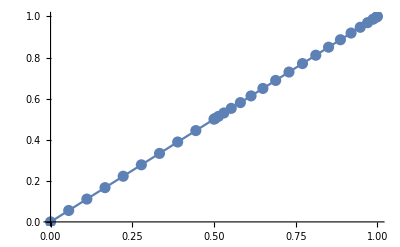

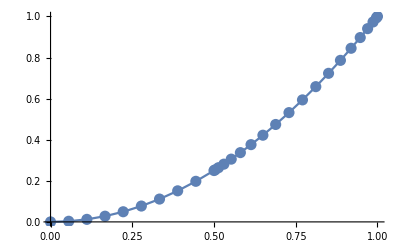

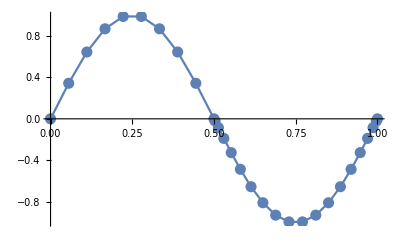

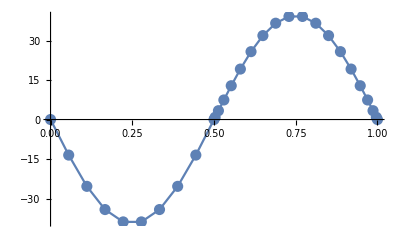

```mathematica
points[plot][points[z]]
points[plot][points[z]^2]
points[plot][Sin[2π points[z]]]
points[plot][points[diff][Sin[2π points[z]],2],PlotRange->All]
```

## Other features

29

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

points[spacing]==0.0555556

InterpolatingFunction[{{0., 1.}}, <>]

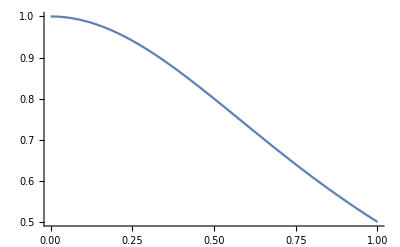

```mathematica
points[number]
points[zeroes]
points[ones]
(* Spacing does not exist for collocation points*)
points[spacing]==points[z][[2]]-points[z][[1]] 
points[interpolation][1/(1+points[z]^2)]
Plot[%[z],{z,0,1}]
```

## Integrate

```mathematica
points[plot][points[integrate][points[ones]]]
```

-Graphics-

## Interpolate and evaluate

```mathematica
points[evaluate][points[z]^2,{0.1,0.2,0.3}]
```

{0.01,0.04,0.09}

## If you have some equation of a function f[z] that you wish to discretise:

```mathematica
z f'[z]+f[z]/.points[substituteAnalytic][{f}]
```

{0.+f[1],f[2]+0.0555556 (-2.25 f[1]-28.6714 f[2]+63. f[3]-63. f[4]+52.5 f[5]-31.5 f[6]+12.6 f[7]-3. f[8]+0.321429 f[9]),f[3]+0.111111 (0.321429 f[1]-5.14286 f[2]-17.1 f[3]+36. f[4]-22.5 f[5]+12. f[6]-4.5 f[7]+1.02857 f[8]-0.107143 f[9]),f[4]+0.166667 (-0.107143 f[1]+1.28571 f[2]-9. f[3]-8.1 f[4]+22.5 f[5]-9. f[6]+3. f[7]-0.642857 f[8]+0.0642857 f[9]),f[5]+0.222222 (0.0642857 f[1]-0.685714 f[2]+3.6 f[3]-14.4 f[4]-5.4956×10^-15 f[5]+14.4 f[6]-3.6 f[7]+0.685714 f[8]-0.0642857 f[9]),f[6]+0.277778 (0.0642857 f[2]-0.685714 f[3]+3.6 f[4]-14.4 f[5]-5.4956×10^-15 f[6]+14.4 f[7]-3.6 f[8]+0.685714 f[9]-0.0642857 f[10]),f[7]+0.333333 (-0.0642857 f[2]+0.642857 f[3]-3. f[4]+9. f[5]-22.5 f[6]+8.1 f[7]+9. f[8]-1.28571 f[9]+0.107143 f[10]),f[8]+0.388889 (0.107143 f[2]-1.02857 f[3]+4.5 f[4]-12. f[5]+22.5 f[6]-36. f[7]+17.1 f[8]+5.14286 f[9]-0.321429 f[10]),f[9]+0.444444 (-0.321429 f[2]+3. f[3]-12.6 f[4]+31.5 f[5]-52.5 f[6]+63. f[7]-63. f[8]+28.6714 f[9]+2.25 f[10]),f[10]+0.5 (-482. f[10]+586.566 f[11]-147.648 f[12]+66.3756 f[13]-37.94 f[14]+24.7894 f[15]-17.658 f[16]+13.3711 f[17]-10.6028 f[18]+8.7201 f[19]-7.38976 f[20]+6.4232 f[21]-5.70737 f[22]+5.17147 f[23]-4.76962 f[24]+4.47142 f[25]-4.25651 f[26]+4.11138 f[27]-4.02746 f[28]+2. f[29]),f[11]+0.50341 (-146.642 f[10]+72.8174 f[11]+98.6581 f[12]-37.4225 f[13]+20.2818 f[14]-12.9416 f[15]+9.10305 f[16]-6.84151 f[17]+5.39902 f[18]-4.42585 f[19]+3.74202 f[20]-3.24716 f[21]+2.88173 f[22]-2.60874 f[23]+2.40436 f[24]-2.25288 f[25]+2.14381 f[26]-2.0702 f[27]+2.02765 f[28]-1.00687 f[29]),f[12]+0.513546 (36.9121 f[10]-98.6581 f[11]+17.9421 f[12]+60.2923 f[13]-25.5303 f[14]+14.8956 f[15]-10.0284 f[16]+7.3513 f[17]-5.71158 f[18]+4.63372 f[19]-3.88955 f[20]+3.35767 f[21]-2.96843 f[22]+2.67959 f[23]-2.46442 f[24]+2.30553 f[25]-2.19143 f[26]+2.11457 f[27]-2.0702 f[28]+1.02785 f[29]),f[13]+0.530132 (-16.5939 f[10]+37.4225 f[11]-60.2923 f[12]+7.76488 f[13]+44.2805 f[14]-19.7832 f[15]+12.0291 f[16]-8.37208 f[17]+6.30927 f[18]-5.01949 f[19]+4.15777 f[20]-3.55568 f[21]+3.12215 f[22]-2.80422 f[23]+2.56945 f[24]-2.3972 f[25]+2.27409 f[26]-2.19143 f[27]+2.14381 f[28]-1.06413 f[29]),f[14]+0.552715 (9.48499 f[10]-20.2818 f[11]+25.5303 f[12]-44.2805 f[13]+4.18357 f[14]+35.7593 f[15]-16.5158 f[16]+10.324 f[17]-7.35761 f[18]+5.66122 f[19]-4.58863 f[20]+3.86613 f[21]-3.35898 f[22]+2.99381 f[23]-2.72773 f[24]+2.5344 f[25]-2.3972 f[26]+2.30553 f[27]-2.25288 f[28]+1.11786 f[29]),f[15]+0.58068 (-6.19735 f[10]+12.9416 f[11]-14.8956 f[12]+19.7832 f[13]-35.7593 f[14]+2.50247 f[15]+30.6905 f[16]-14.5145 f[17]+9.26363 f[18]-6.72606 f[19]+5.26412 f[20]-4.33479 f[21]+3.70722 f[22]-3.26736 f[23]+2.95298 f[24]-2.72773 f[25]+2.56945 f[26]-2.46442 f[27]+2.40436 f[28]-1.19241 f[29]),f[16]+0.613263 (4.41451 f[10]-9.10305 f[11]+10.0284 f[12]-12.0291 f[13]+16.5158 f[14]-30.6905 f[15]+1.56082 f[16]+27.5382 f[17]-13.2686 f[18]+8.61384 f[19]-6.35397 f[20]+5.04774 f[21]-4.21655 f[22]+3.65665 f[23]-3.26736 f[24]+2.99381 f[25]-2.80422 f[26]+2.67959 f[27]-2.60874 f[28]+1.29287 f[29]),f[17]+0.649576 (-3.34278 f[10]+6.84151 f[11]-7.3513 f[12]+8.37208 f[13]-10.324 f[14]+14.5145 f[15]-27.5382 f[16]+0.957968 f[17]+25.6066 f[18]-12.5346 f[19]+8.25977 f[20]-6.18065 f[21]+4.9789 f[22]-4.21655 f[23]+3.70722 f[24]-3.35898 f[25]+3.12215 f[26]-2.96843 f[27]+2.88173 f[28]-1.42684 f[29]),f[18]+0.688629 (2.65071 f[10]-5.39902 f[11]+5.71158 f[12]-6.30927 f[13]+7.35761 f[14]-9.26363 f[15]+13.2686 f[16]-25.6066 f[17]+0.522456 f[18]+24.554 f[19]-12.1927 f[20]+8.14712 f[21]-6.18065 f[22]+5.04774 f[23]-4.33479 f[24]+3.86613 f[25]-3.55568 f[26]+3.35767 f[27]-3.24716 f[28]+1.6058 f[29]),f[19]+0.729355 (-2.18003 f[10]+4.42585 f[11]-4.63372 f[12]+5.01949 f[13]-5.66122 f[14]+6.72606 f[15]-8.61384 f[16]+12.5346 f[17]-24.554 f[18]+0.166293 f[19]+24.2191 f[20]-12.1927 f[21]+8.25977 f[22]-6.35397 f[23]+5.26412 f[24]-4.58863 f[25]+4.15777 f[26]-3.88955 f[27]+3.74202 f[28]-1.84744 f[29]),f[20]+0.770645 (1.84744 f[10]-3.74202 f[11]+3.88955 f[12]-4.15777 f[13]+4.58863 f[14]-5.26412 f[15]+6.35397 f[16]-8.25977 f[17]+12.1927 f[18]-24.2191 f[19]-0.166293 f[20]+24.554 f[21]-12.5346 f[22]+8.61384 f[23]-6.72606 f[24]+5.66122 f[25]-5.01949 f[26]+4.63372 f[27]-4.42585 f[28]+2.18003 f[29]),f[21]+0.811371 (-1.6058 f[10]+3.24716 f[11]-3.35767 f[12]+3.55568 f[13]-3.86613 f[14]+4.33479 f[15]-5.04774 f[16]+6.18065 f[17]-8.14712 f[18]+12.1927 f[19]-24.554 f[20]-0.522456 f[21]+25.6066 f[22]-13.2686 f[23]+9.26363 f[24]-7.35761 f[25]+6.30927 f[26]-5.71158 f[27]+5.39902 f[28]-2.65071 f[29]),f[22]+0.850424 (1.42684 f[10]-2.88173 f[11]+2.96843 f[12]-3.12215 f[13]+3.35898 f[14]-3.70722 f[15]+4.21655 f[16]-4.9789 f[17]+6.18065 f[18]-8.25977 f[19]+12.5346 f[20]-25.6066 f[21]-0.957968 f[22]+27.5382 f[23]-14.5145 f[24]+10.324 f[25]-8.37208 f[26]+7.3513 f[27]-6.84151 f[28]+3.34278 f[29]),f[23]+0.886737 (-1.29287 f[10]+2.60874 f[11]-2.67959 f[12]+2.80422 f[13]-2.99381 f[14]+3.26736 f[15]-3.65665 f[16]+4.21655 f[17]-5.04774 f[18]+6.35397 f[19]-8.61384 f[20]+13.2686 f[21]-27.5382 f[22]-1.56082 f[23]+30.6905 f[24]-16.5158 f[25]+12.0291 f[26]-10.0284 f[27]+9.10305 f[28]-4.41451 f[29]),f[24]+0.91932 (1.19241 f[10]-2.40436 f[11]+2.46442 f[12]-2.56945 f[13]+2.72773 f[14]-2.95298 f[15]+3.26736 f[16]-3.70722 f[17]+4.33479 f[18]-5.26412 f[19]+6.72606 f[20]-9.26363 f[21]+14.5145 f[22]-30.6905 f[23]-2.50247 f[24]+35.7593 f[25]-19.7832 f[26]+14.8956 f[27]-12.9416 f[28]+6.19735 f[29]),f[25]+0.947285 (-1.11786 f[10]+2.25288 f[11]-2.30553 f[12]+2.3972 f[13]-2.5344 f[14]+2.72773 f[15]-2.99381 f[16]+3.35898 f[17]-3.86613 f[18]+4.58863 f[19]-5.66122 f[20]+7.35761 f[21]-10.324 f[22]+16.5158 f[23]-35.7593 f[24]-4.18357 f[25]+44.2805 f[26]-25.5303 f[27]+20.2818 f[28]-9.48499 f[29]),f[26]+0.969868 (1.06413 f[10]-2.14381 f[11]+2.19143 f[12]-2.27409 f[13]+2.3972 f[14]-2.56945 f[15]+2.80422 f[16]-3.12215 f[17]+3.55568 f[18]-4.15777 f[19]+5.01949 f[20]-6.30927 f[21]+8.37208 f[22]-12.0291 f[23]+19.7832 f[24]-44.2805 f[25]-7.76488 f[26]+60.2923 f[27]-37.4225 f[28]+16.5939 f[29]),f[27]+0.986454 (-1.02785 f[10]+2.0702 f[11]-2.11457 f[12]+2.19143 f[13]-2.30553 f[14]+2.46442 f[15]-2.67959 f[16]+2.96843 f[17]-3.35767 f[18]+3.88955 f[19]-4.63372 f[20]+5.71158 f[21]-7.3513 f[22]+10.0284 f[23]-14.8956 f[24]+25.5303 f[25]-60.2923 f[26]-17.9421 f[27]+98.6581 f[28]-36.9121 f[29]),f[28]+0.99659 (1.00687 f[10]-2.02765 f[11]+2.0702 f[12]-2.14381 f[13]+2.25288 f[14]-2.40436 f[15]+2.60874 f[16]-2.88173 f[17]+3.24716 f[18]-3.74202 f[19]+4.42585 f[20]-5.39902 f[21]+6.84151 f[22]-9.10305 f[23]+12.9416 f[24]-20.2818 f[25]+37.4225 f[26]-98.6581 f[27]-72.8174 f[28]+146.642 f[29]),f[29]+1. (-2. f[10]+4.02746 f[11]-4.11138 f[12]+4.25651 f[13]-4.47142 f[14]+4.76962 f[15]-5.17147 f[16]+5.70737 f[17]-6.4232 f[18]+7.38976 f[19]-8.7201 f[20]+10.6028 f[21]-13.3711 f[22]+17.658 f[23]-24.7894 f[24]+37.94 f[25]-66.3756 f[26]+147.648 f[27]-586.566 f[28]+482. f[29])}

# Points2D

```mathematica
Clear[zPoints,vPoints,points2D,func2D];
CollocationPointsFactory[zPoints,-1,1,10,z,Precision->MachinePrecision];
CollocationPointsFactory[vPoints,0,1,5,v,Precision->MachinePrecision];
CollocationPoints2DFactory[points2D,zPoints[z],vPoints[v],z,v,Precision->MachinePrecision];

func2D=Outer[Function[{z,v}, Sin[z]],points2D[z],points2D[v]];
```

```mathematica
points2D[zeroes]//MatrixForm
points2D[ones]//MatrixForm
points2D[grid][z]//MatrixForm
points2D[grid][v]//MatrixForm
```

(0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

(1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1.)

(-1. | -1. | -1. | -1. | -1.
-0.939693 | -0.939693 | -0.939693 | -0.939693 | -0.939693
-0.766044 | -0.766044 | -0.766044 | -0.766044 | -0.766044
-0.5 | -0.5 | -0.5 | -0.5 | -0.5
-0.173648 | -0.173648 | -0.173648 | -0.173648 | -0.173648
0.173648 | 0.173648 | 0.173648 | 0.173648 | 0.173648
0.5 | 0.5 | 0.5 | 0.5 | 0.5
0.766044 | 0.766044 | 0.766044 | 0.766044 | 0.766044
0.939693 | 0.939693 | 0.939693 | 0.939693 | 0.939693
1. | 1. | 1. | 1. | 1.)

(0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.
0. | 0.146447 | 0.5 | 0.853553 | 1.)

```mathematica
points2D[plot][func2D]
points2D[plot][points2D[diff][1,0][func2D]]
points2D[plot][Partition[points2D[diffMatrix][1,0].Flatten[func2D],points2D[number][v]]]
points2D[plot][points2D[diff][0,1][func2D]//Chop]

points2D[plot][points2D[diff][1,0][points2D[grid][z]]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

```mathematica
z^2 f[z,v]/.points2D[substituteAnalytic][{f}]//MatrixForm
v^2 f[z,v]/.points2D[substituteAnalytic][{f}]//MatrixForm
```

(1. f[1,1] | 1. f[1,2] | 1. f[1,3] | 1. f[1,4] | 1. f[1,5]
0.883022 f[2,1] | 0.883022 f[2,2] | 0.883022 f[2,3] | 0.883022 f[2,4] | 0.883022 f[2,5]
0.586824 f[3,1] | 0.586824 f[3,2] | 0.586824 f[3,3] | 0.586824 f[3,4] | 0.586824 f[3,5]
0.25 f[4,1] | 0.25 f[4,2] | 0.25 f[4,3] | 0.25 f[4,4] | 0.25 f[4,5]
0.0301537 f[5,1] | 0.0301537 f[5,2] | 0.0301537 f[5,3] | 0.0301537 f[5,4] | 0.0301537 f[5,5]
0.0301537 f[6,1] | 0.0301537 f[6,2] | 0.0301537 f[6,3] | 0.0301537 f[6,4] | 0.0301537 f[6,5]
0.25 f[7,1] | 0.25 f[7,2] | 0.25 f[7,3] | 0.25 f[7,4] | 0.25 f[7,5]
0.586824 f[8,1] | 0.586824 f[8,2] | 0.586824 f[8,3] | 0.586824 f[8,4] | 0.586824 f[8,5]
0.883022 f[9,1] | 0.883022 f[9,2] | 0.883022 f[9,3] | 0.883022 f[9,4] | 0.883022 f[9,5]
1. f[10,1] | 1. f[10,2] | 1. f[10,3] | 1. f[10,4] | 1. f[10,5])

(0. | 0.0214466 f[1,2] | 0.25 f[1,3] | 0.728553 f[1,4] | 1. f[1,5]
0. | 0.0214466 f[2,2] | 0.25 f[2,3] | 0.728553 f[2,4] | 1. f[2,5]
0. | 0.0214466 f[3,2] | 0.25 f[3,3] | 0.728553 f[3,4] | 1. f[3,5]
0. | 0.0214466 f[4,2] | 0.25 f[4,3] | 0.728553 f[4,4] | 1. f[4,5]
0. | 0.0214466 f[5,2] | 0.25 f[5,3] | 0.728553 f[5,4] | 1. f[5,5]
0. | 0.0214466 f[6,2] | 0.25 f[6,3] | 0.728553 f[6,4] | 1. f[6,5]
0. | 0.0214466 f[7,2] | 0.25 f[7,3] | 0.728553 f[7,4] | 1. f[7,5]
0. | 0.0214466 f[8,2] | 0.25 f[8,3] | 0.728553 f[8,4] | 1. f[8,5]
0. | 0.0214466 f[9,2] | 0.25 f[9,3] | 0.728553 f[9,4] | 1. f[9,5]
0. | 0.0214466 f[10,2] | 0.25 f[10,3] | 0.728553 f[10,4] | 1. f[10,5])

```mathematica
points2D[diff][1,0][points2D[grid][z]]
Partition[points2D[diffMatrix][1,0].Flatten[points2D[grid][z]],points2D[number][v]]

points2D[diff][0,1][points2D[grid][v]]
Partition[points2D[diffMatrix][0,1].Flatten[points2D[grid][v]],points2D[number][v]]
```

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

{{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.},{1.,1.,1.,1.,1.}}

«1 more identical outputs»